```mathematica
WolframModelObjectProperties[x_WolframModelEvolutionObject] := {x["FinalStatePlot"],
 ListLinePlot[x["VertexCountList"]],
 ListLinePlot[x["EdgeCountList"]], 
 ListLinePlot[Map[GraphDiameter, Map[UndirectedGraph, Map[ResourceFunction["HypergraphToGraph"],x["StatesList"]]]]], ResourceFunction["ConnectedHypergraphQ"][x["FinalState"]]}
```

```mathematica
WolframModelObjectProperties :: usage = "WolframModelObjectProperties takes a WolframModelEvolutionObject as an input. It gives the list of: its Final State Plot, Line Plot of its final vertex and edge counts, plot of diameter at all states, and whether the hypergraph is connected or not.";
```

```mathematica
WolframModelRuleGrowth[x_, y_, z_Integer] := Flatten[{RulePlot[ResourceFunction["WolframModel"][x]],
ResourceFunction["WolframModelPlot"][y], z, 
WolframModelObjectProperties[ResourceFunction["WolframModel"][x, y, z]]}, 1]
```

```mathematica
WolframModelRuleGrowth::usage = "WolframModelRuleGrowth takes an input of a rule (x), initial hypergraph (y), and number of steps (z) - in the same order. It returns a list of Rule Plot, Plot of Initial Hypergraph, number of steps, and the output of WolframModelObjectProperties for the WolframModelEvolutionObject produced by the rule (x) applied on initial hypergraph (y) for z steps.";
```

```mathematica
WolframModelSignatureGrowth[x_] := Column[Table[WolframModelRuleGrowth[i, Keys[i], 10],
{i, ResourceFunction["EnumerateWolframModelRules"][x]}]]
```

```mathematica
WolframModelSignatureGrowth::usage = "WolframModelSignatureGrowth takes a signature (x) as an input. It gives the table of the outputs of WolframModelRuleGrowth applied to each rule produced by EnumerateWolframModelRules[x]. The number of steps is 10, and the initial hypergraph is the same as the LHS of the Rule.";
```

```mathematica
WolframModelSignGrowthCon[x_] := Column[Table[If[ResourceFunction["ConnectedHypergraphQ"]
[ResourceFunction["WolframModel"][i, Keys[i], 3, "FinalState"]] && 
Length@ResourceFunction["WolframModel"][i, Keys[i], 3, "EdgeCountList"] > 2, 
WolframModelRuleGrowth[i, Keys[i], 10], Nothing],
{i, ResourceFunction["EnumerateWolframModelRules"][x]}]]
```

```mathematica
WolframModelSignGrowthCon::usage = "WolframModelSignGrowthCon takes in a signature and returns the output of WolframModelSignatureGrowth minus the rules for which the hypergraph at 3rd step is disconnected or does not grow after 3 steps.";
```

```mathematica
GrowthRateDataLocal = FileNameJoin[{Directory[], "GrowthRateData.wl"}]
```

D:\Jatin Kansal\Wolfram Project\GrowthRateData.wl

```mathematica
WolframModelSignGrowthCon[{{1,2}} -> {{2,2}}]
```

```mathematica
Sign1222Con = WolframModelSignGrowthCon[{{1,2}} -> {{2,2}}]
```

```mathematica
Save[GrowthRateDataLocal, Sign1222Con];
```

```mathematica
Sign1222 = WolframModelSignatureGrowth[{{1,2}}->{{2,2}}]
```

```mathematica
Save[GrowthRateDataLocal, Sign1222]
```

```mathematica
eo=ResourceFunction["WolframModel"][{{1,2,3}}->{{1,2},{2,3,4},{1,4}},Automatic,Automatic]
```

WolframModelEvolutionObject[…]

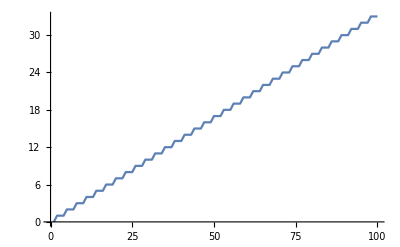

```mathematica
ListLinePlot[Map[GraphDiameter, Map[UndirectedGraph, Map[ResourceFunction["HypergraphToGraph"],eo["StatesList"]]]]]
```

```mathematica
eo["StatesList"]
```

{{{1,1,1}},98,{{1,1},{1,2},{1,1},{1,3},{1,2},{1,4},{2,3},{2,5},{3,4},{3,6},{4,5},{4,7},{5,6},{5,8},{6,7},{6,9},{7,8},{7,10},{8,9},{8,11},{9,10},{9,12},{10,11},{10,13},{11,12},{11,14},{12,13},{12,15},{13,14},{13,16},{14,15},{14,17},{15,16},133,{82,83},{82,85},{83,84},{83,86},{84,85},{84,87},{85,86},{85,88},{86,87},{86,89},{87,88},{87,90},{88,89},{88,91},{89,90},{89,92},{90,91},{90,93},{91,92},{91,94},{92,93},{92,95},{93,94},{93,96},{94,95},{94,97},{95,96},{95,98},{96,97},{96,99},{97,98},{98,99,100},{97,100}}}
 |  |  |  |

```mathematica
ResourceFunction["ConnectedHypergraphQ"]@eo["FinalState"]
```

True

```mathematica
EvenQ@2
```

True